```mathematica
g1=Exp[-r^2/3^2];
g2=Exp[-r^2/5^2];
```

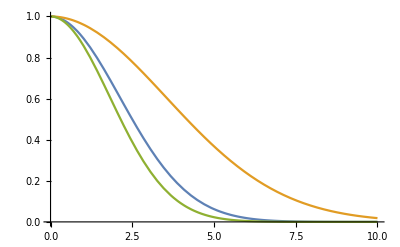

```mathematica
Plot[{g1,g2,g1*g2},{r,0,10}]
```

```mathematica
Exp[-1]//N
```

0.367879

```mathematica
Solve[r^2/3^2+r^2/5^2==1,r]//N
```

{{r→-2.57248},{r→2.57248}}

```mathematica
InverseFourierTransform[ⅇ^((ⅈ*kp^2*z)/k),kp,r]
```

(ⅇ^(-(ⅈ k r^2)/(4 z)))/(√2 √(-(ⅈ z)/k))

```mathematica
FourierTransform[Exp[(-ⅈ*k*r^2)/(2z)],r,kp]
```

(ⅇ^((ⅈ kp^2 z)/(2 k)))/(√((ⅈ k)/z))